The following example comes from Example 5.3.1 in Connelly, SIAM J. Discrete Math., 9, 453-491 (1996)

This 3D framework is second-order rigid but not prestress stable. Vertex 2 is on top of 7 and vertex 4 is on top of 8. To avoid identifying these two pairs of vertices with each other, we will add a small displacement to vertices 7 and 8. We define pos below for the correct vertex positions.

```mathematica
m=Linkage[{
{0,0,0},{0,1,0},{0,0,1},
{1,0,0},{1,1,0},{0,1+0.01,0},{1+0.01,0,0}
},{
RigidBar[{
{1,2},{1,3},{1,4},{1,6},{1,7},{2,3},{2,5},{2,7},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7}
},"shape"->RigidBarShape["width"->0.003]],
PinnedJoint[1],
Property[PinnedJoint[2],"constraint"->(#[[{1,3}]]&) ],Property[PinnedJoint[3],"constraint"->(#[[1]]&)]
}
]
pos={{0,0,0},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,0},{1,0,0}};
```

-Graphics3D-

There are two self stresses and two zero modes

```mathematica
ss=MechanismSelfStresses[m,pos]
zm=MechanismZeroModes[m,pos]
```

{{1,0,0,-1,0,0,1,-1,0,0,0,0,-1,0,1,0,0,0,0,0,0},{1,0,-1,-1,1,0,1,-1,0,0,-1,1,-1,1,0,0,0,0,0,0,0}}

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,0}}}

The linear zero modes and quadratic constraints associated with them.

```mathematica
eq=MechanismInfinitesimalMotions[m,pos,"variables"->v]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,v[2]},{0,0,v[1]}},{√(2/3) v[1] v[2]+v[2]^2/(√6),-√(6/35) v[1]^2-√(10/21) v[1] v[2]+v[2]^2/(√210)}}

The system is second order rigid.

```mathematica
Solve[eq[[2]]==0,{v[1],v[2]}]
```

{{v[1]→0,v[2]→0},{v[1]→0,v[2]→0}}

There is no linear combination of the two quadratic forms that is positive definite. This is equivalent to the mechanism not being prestress stable.

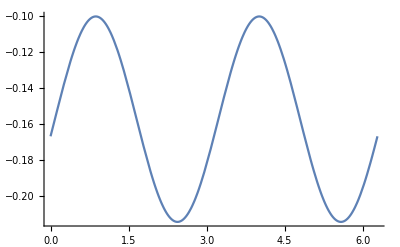

```mathematica
mat=Normal@CoefficientArrays[#,{v[1],v[2]},Symmetric->True][[3]]&/@eq[[2]];
Plot[Det[Cos[t] mat[[1]]+Sin[t] mat[[2]]],{t,0,2Pi}]
```